## Load and Prepare Audio for Feature Extraction

Audio are loaded, resampled to 16 Khz , and chunked to 0.96s windows (both required by YAMNet).

```mathematica
(* Define the directories *)
nopoiDirectory="/Users/jcromwell/Library/CloudStorage/GoogleDrive-jcromwell@entacmedical.com/Shared drives/*Master Drive - ABJ/*Master Folder - Entac/R&D/PrevisAI/files/12h/nopoi/foreground";
poiDirectory="/Users/jcromwell/Library/CloudStorage/GoogleDrive-jcromwell@entacmedical.com/Shared drives/*Master Drive - ABJ/*Master Folder - Entac/R&D/PrevisAI/files/12h/poi/foreground";

(* Get the list of audio files *)
nopoiFiles=FileNames["*.wav",nopoiDirectory];
poiFiles=FileNames["*.wav",poiDirectory];

(*Convert to single channel and resample at 16KHz*)
resampledNoPOI=AudioResample[AudioChannelMix[Import[#],"Mono"],16000]&/@nopoiFiles;
resampledPOI=AudioResample[AudioChannelMix[Import[#],"Mono"],16000]&/@poiFiles;
```

## Feature Extractor

```mathematica
(*Import AudioIdentify V1 which is trained on same set as YAMNet*)
(*Modify the model for feature extraction*)
coreNet=NetExtract[NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"],{1,"Net"}];
singleFrameFeatureExtractor=NetDrop[coreNet,-3];
extractor=NetChain[{NetMapOperator[singleFrameFeatureExtractor],AggregationLayer[Max,1],FlattenLayer[]},"Input"->NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data"][["Input"]]];
```

## Feature Extraction

```mathematica
featureVectorsPOI=extractor[resampledPOI,TargetDevice->"GPU"];
poiData=Thread[featureVectorsPOI->1];
```

```mathematica
featureVectorsNoPOI=extractor[resampledNoPOI,TargetDevice->"GPU"];
nopoiData=Thread[featureVectorsNoPOI->0];
```

```mathematica
Length@poiData
Length@nopoiData
```

17

73

## Stratified Split of Data

```mathematica
SeedRandom[];
stratifiedSplitFromGroups[poiData_List,nopoiData_List,poiTestCount_Integer:5]:=Module[{shuffledPOI,shuffledNoPOI,poiTrainFeatures,poiTestFeatures,noPoiTrainFeatures,noPoiTestFeatures,noPoiTestCount,trainPairs,testPairs,shuffledTrain,shuffledTest,xTrain,yTrain,xTest,yTest},(*1. Split the POI data (labeled 1)*)shuffledPOI=RandomSample[poiData];
poiTestFeatures=Take[shuffledPOI,poiTestCount];
poiTrainFeatures=Drop[shuffledPOI,poiTestCount];
(*2. Split the non-POI data (labeled 0) using the same proportion*)noPoiTestCount=Round[Length[nopoiData]*(Length[poiTestFeatures]/Length[poiData])];
shuffledNoPOI=RandomSample[nopoiData];
noPoiTestFeatures=Take[shuffledNoPOI,noPoiTestCount];
noPoiTrainFeatures=Drop[shuffledNoPOI,noPoiTestCount];
(*3. Create {feature,label} pairs for the training and test sets*)trainPairs=Join[Transpose[{poiTrainFeatures,ConstantArray[1,Length[poiTrainFeatures]]}],Transpose[{noPoiTrainFeatures,ConstantArray[0,Length[noPoiTrainFeatures]]}]];
testPairs=Join[Transpose[{poiTestFeatures,ConstantArray[1,Length[poiTestFeatures]]}],Transpose[{noPoiTestFeatures,ConstantArray[0,Length[noPoiTestFeatures]]}]];
(*4. Shuffle the pairs and separate back into features (X) and labels (y)*){xTrain,yTrain}=Transpose[RandomSample[trainPairs]];
{xTest,yTest}=Transpose[RandomSample[testPairs]];
(*5. Return an Association for clarity*)<|"XTrain"->xTrain,"yTrain"->yTrain,"XTest"->xTest,"yTest"->yTest|>];
poiFeatureVectors=First/@poiData;
nopoiFeatureVectors=First/@nopoiData;
splitData=stratifiedSplitFromGroups[poiFeatureVectors,nopoiFeatureVectors,5];
trainingData=Thread[splitData["XTrain"]->splitData["yTrain"]];
testData=Thread[splitData["XTest"]->splitData["yTest"]];
```

## Train Model

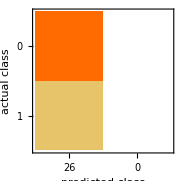
Classifier Measurements
Classifier method | GradientBoostedTrees
Number of test examples | 26
Accuracy | (81.8.) %
Accuracy baseline | (81.8.) %
Geometric mean of probabilities | 0.613 ± 0.071
Mean cross entropy | 0.49 ± 0.12
Single evaluation time | 4.48 ms/example
Batch evaluation speed | 1.46 examples/ms
-Graphics- |

```mathematica
utf=UtilityFunction-> <|0-> <|0-> 1, 1-> -1|>,1-> <|1-> 1,0->-2|>|>;
classifier=Classify[trainingData,Method->"GradientBoostedTrees",TargetDevice->"CPU",PerformanceGoal->"Quality",utf];
measurements=ClassifierMeasurements[classifier,testData]
```